## Губка Менгера

```mathematica
carpet[0]:={{1,1,1},{1,1,1},{1,1,1}}
```

```mathematica
carpet[n_]:=Nest[ArrayFlatten[{{#,#,#},{#,0,#},{#,#,#}}]&,1,n]
```


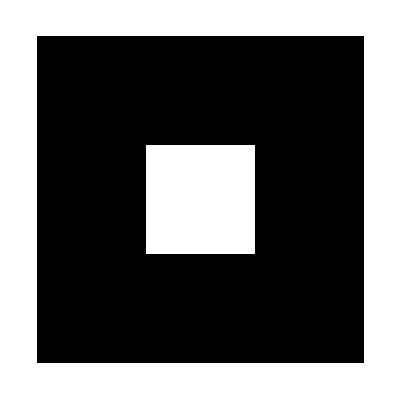
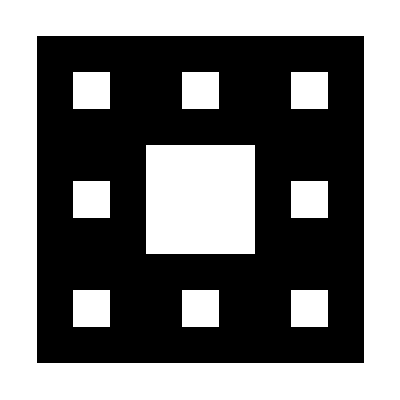
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ArrayPlot[carpet[t]],{t,0,4}]
```

```mathematica
carpet3D[0]:={{{1,1,1},{1,1,1},{1,1,1}},{{1,1,1},{1,1,1},{1,1,1}},{{1,1,1},{1,1,1},{1,1,1}}}
```

```mathematica
carpet3D[n_]:=Nest[ArrayFlatten[{{{#,#,#},{#,0,#},{#,#,#}},{{#,0,#},{0,0,0},{#,0,#}},{{#,#,#},{#,0,#},{#,#,#}}},3]&,1,n];
```

```mathematica
Table[Graphics3D[{RandomColor[],Cuboid/@Position[carpet3D@t,1]}],{t,0,4}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

## Кривая Пеано

```mathematica
Peano={{0.,0.},{0.,1.},{0.,2.},{1.,2.},{1.,1.},{1.,0.},{2.,0.},{2.,1.},{2.,2.}};
```

```mathematica
PeanoSquare[list_]:=Block[{k,p, r1,p1,new},
r1=(Last[list]⟦1⟧-First[list]⟦1⟧)*2+1;
k=Reverse[{0,r1}+#&/@(list//ReflectionTransform[{0,1}])];
p=Join[list,k,{0,r1+1}+#&/@list];
p1=Reverse[{r1,0}+#&/@(p//ReflectionTransform[{1,0}])];
new={r1+1,0}+#&/@p;
Join[Join[p,p1,new]]
]
```

```mathematica
PeanoFunc[Peano,0]:=Graphics[Line[Peano]]
```

```mathematica
PeanoFunc[list_,n_]:=Graphics[Line[Nest[PeanoSquare[#]&,list,n]]]
```

```mathematica
Table[PeanoFunc[Peano,t],{t,1,3}]
```

## Кривая Дракона

```mathematica
func[list_]:=Join[list,Reverse@(RotationTransform[90Degree,Last@list]/@list)//Delete[#,1]&]
```

```mathematica
f[n_,list_]:=Nest[func,list,n]
```

```mathematica
Table[PeanoFunc[Peano,t],{t,1,3}]
```